```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions=r>=0&&Q>=0&&M>0&&α>0;
SetDirectory[FileNameJoin[{NotebookDirectory[],"Imágenes"}]];
tickfunc[xmin_,xmax_]:=Table[{x,NumberForm[x,20]},{x,xmin,xmax,(xmax-xmin)/4}];
ℱRNac=(1−(2M)/r+Q^2/r^2)(1−ξ((2M)/r−Q^2/r^2) (1−(2M)/r+Q^2/r^2));
ℱRNac1=(1−(2M)/r+Q^2/r^2);
ℱRNac2=(1−ξ((2M)/r−Q^2/r^2) (1−(2M)/r+Q^2/r^2));
ℱ[M_]:=(1−(2M)/r)(1−ξ((2M)/r) (1−(2M)/r));
ℱ1[M_]:=(1−(2M)/r);
ℱ2[M_]:=(1−ξ((2M)/r) (1−(2M)/r));
MRN=M;
MDEC=M(1-1/((1+((2 M r)/Q^2)^3)^(1/3)));
MABG=M (r^3/((r^2+Q^2)^(3/2))-(Q^2 r^3)/(2M(r^2+Q^2)^2));
Mtanh=M (1-Tanh[Q^2/(2 M r)]);
Mexp=M Exp[-Q^2/(2M r)];
ξmaxw=ξ/.Solve[ℱRNac==0,ξ]//FullSimplify;
ξDEC=ξ/.Solve[ℱ[MDEC]==0,ξ]//FullSimplify;
ξABG=ξ/.Solve[ℱ[MABG]==0,ξ]//FullSimplify;
ξtanh=ξ/.Solve[ℱ[Mtanh]==0,ξ]//FullSimplify;
ξexp=ξ/.Solve[ℱ[Mexp]==0,ξ]//FullSimplify;
Cond2[M_]:=2/r D[(M), r]-D[(D[(M), r]), r]
Cond3[M_]:=2/r D[(M), r]+D[(D[M, r]), r];
Mα=((MDEC α) +(MABG(1-α)))//FullSimplify;
```

## Mezcla

```mathematica
ℱ1[Mα]//FullSimplify
Series[%,{r,∞,6}]//Simplify
```

1-(2 (M (-(Q^2 r^3)/(2 M (Q^2+r^2)^2)+r^3/((Q^2+r^2)^(3/2))) (1-α)+M (1-1/((1+(8 M^3 r^3)/Q^6)^(1/3))) α))/r

1-(2 M)/r+Q^2/r^2-(3 (M Q^2 (-1+α)))/r^3+(2 Q^4 (-1+α))/r^4+(15/4 M Q^4 (-1+α)-(Q^8 α)/(24 M^3))/r^5-(3 (Q^6 (-1+α)))/r^6+O[1/r]^7

```mathematica
α/.NSolve[(ℱ[Mα]/.{M->1,Q->0.8,ξ->5})==0,α][[1]]
```

$Aborted

{0.999993,0.999926}

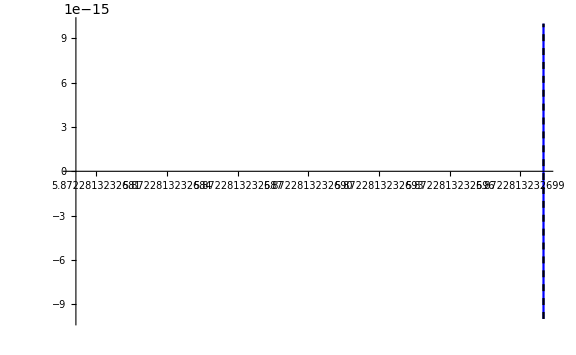

```mathematica
ini={1.866024,5.872281323268,0};
fin={1.866041,5.87228132327,10};
αX={.99999346463,.9999255}
parameter={M->1,Q->0.5,ξ->4.5,α->αX[[1]]};
Plot[{ℱ[Mα]/.parameter,ℱ[MDEC]/.parameter,ℱRNac/.parameter},{r,ini[[2]],fin[[2]]},PlotRange->{-10^-14,10^-14},PlotStyle->{Blue,Red,{Black,Dashed}},ImageSize->Large]
```

### Condiciones

#### Condición 3

```mathematica
𝒢Mα3=Cond3[Mα]//FullSimplify
%/.α->1//FullSimplify
```

Q^2 r (-6/((Q^2+r^2)^2)+(12 r^4 (-1+α))/((Q^2+r^2)^4)-(3 M (4 Q^2-r^2) (-1+α))/((Q^2+r^2)^(7/2))-(18 r^2 (-1+α))/((Q^2+r^2)^3)+(6 α)/((Q^2+r^2)^2)-(256 M^7 r^3 α)/((Q^6+8 M^3 r^3)^(7/3))+(32 M^4 α)/((Q^6+8 M^3 r^3)^(4/3)))

(32 M^4 Q^8 r)/((Q^6+8 M^3 r^3)^(7/3))

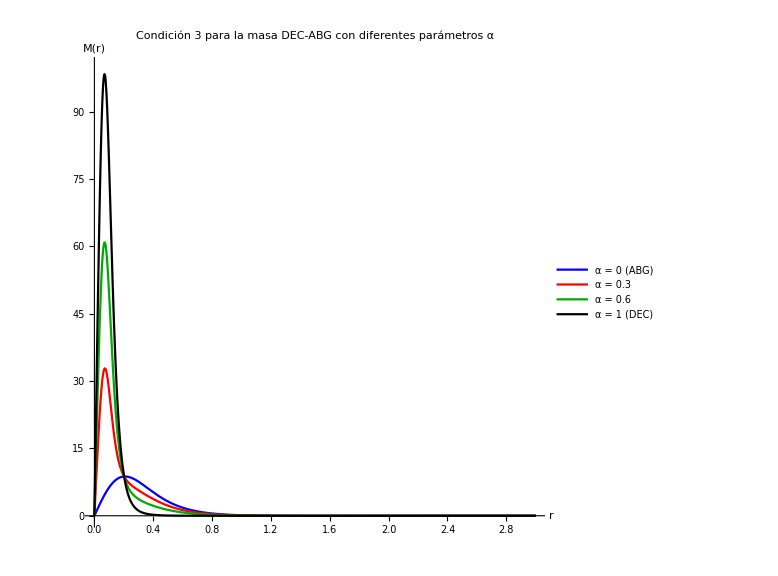
-Graphics-M = 1, Q = 0.5

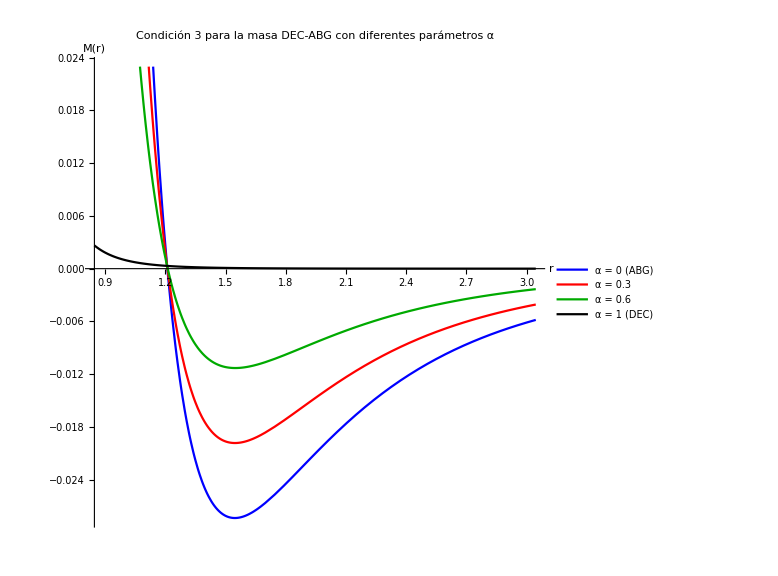
-Graphics-M = 1, Q = 0.5

```mathematica
parameter={M->1,Q->0.5};
alfas={0,.3,.6,1};
titulo="Condición 3 para la masa DEC-ABG con diferentes parámetros α";
leyenda={StringReplace["α = Xα (ABG)",{"Xα"->ToString[alfas[[1]]]}],StringReplace["α = Xα",{"Xα"->ToString[alfas[[2]]]}],StringReplace["α = Xα",{"Xα"->ToString[alfas[[3]]]}],StringReplace["α = Xα (DEC)",{"Xα"->ToString[alfas[[4]]]}]};
label=StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}];
style={{Blue},{Red},{Darker@Green},Black};
plotF={𝒢Mα3/.parameter/.α->alfas[[1]],𝒢Mα3/.parameter/.α->alfas[[2]],𝒢Mα3/.parameter/.α->alfas[[3]],𝒢Mα3/.parameter/.α->alfas[[4]]};
rMin=r/.NMinimize[{𝒢Mα3/.parameter/.α->0,r>0},r][[2]];

ini=0;
fin=3;
Labeled[Plot[plotF,{r,ini,fin},PlotRange->{-.5,100},AspectRatio->1,PlotStyle->style,PlotLabel->titulo,PlotLegends->leyenda,AxesLabel->{"r","M(r)"},ImageSize->Large],label]
Export["Masa_3cond_mezcla_alfa.png",%,"PNG"];
ini=rMin-.7;
fin=rMin+1.5;
Labeled[Plot[plotF,{r,ini,fin},AspectRatio->1,PlotStyle->style,PlotLabel->titulo,PlotLegends->leyenda,AxesLabel->{"r","M(r)"},ImageSize->Large],label]
Export["Masa_3cond_mezcla_alfa_zoomNegativo.png",%,"PNG"];
```

((12 Q^2 r^5)/((Q^2+r^2)^4)-(3 M Q^2 r (4 Q^2-r^2))/((Q^2+r^2)^(7/2))-(18 Q^2 r^3)/((Q^2+r^2)^3)+(6 Q^2 r)/((Q^2+r^2)^2))/((12 Q^2 r^5)/((Q^2+r^2)^4)-(3 M Q^2 r (4 Q^2-r^2))/((Q^2+r^2)^(7/2))-(18 Q^2 r^3)/((Q^2+r^2)^3)+(6 Q^2 r)/((Q^2+r^2)^2)-(256 M^7 Q^2 r^4)/((Q^6+8 M^3 r^3)^(7/3))+(32 M^4 Q^2 r)/((Q^6+8 M^3 r^3)^(4/3)))

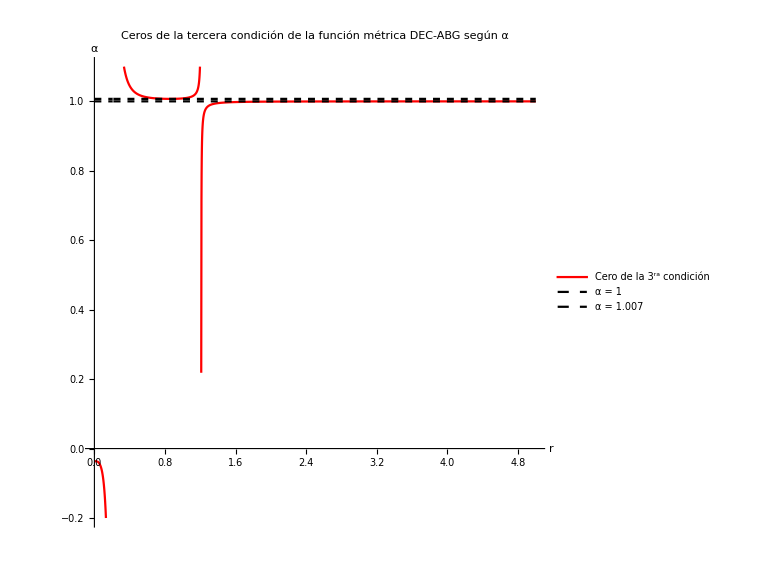
-Graphics-M = 1, Q = 0.5

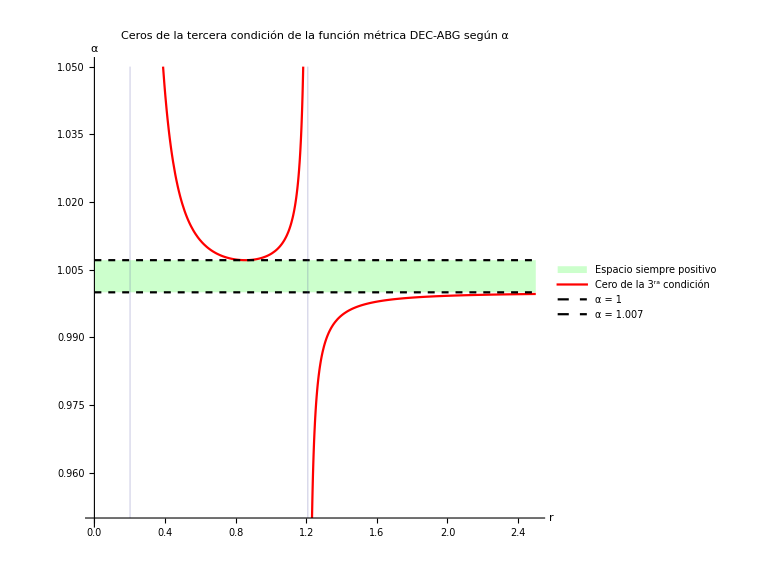
-Graphics-M = 1, Q = 0.5

```mathematica
parameter={M->1,Q->.5};
αminmax3=α/.NSolve[𝒢Mα3==0,α][[1]]//Rationalize

Labeled[Plot[{αminmax3/.parameter,1, 1.0071215317999305},{r,0,5},PlotRange->{-.2,1.1},Exclusions->{(αminmax3/.parameter)==5},PlotStyle->{Red,{Black,Dashed},{Black,Dashed}},AspectRatio->1,PlotLabel->"Ceros de la tercera condición de la función métrica DEC-ABG según α",PlotLegends->{"Cero de la 3^ra condición","α = 1","α = 1.007"},AxesLabel->{"r","α"},ImageSize->Large],StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}]]
Export["Soluciones_3raCond_Alfa_Mezcla.png",%,"PNG"];

Legended[Labeled[Plot[{αminmax3/.parameter,1, 1.0071215317999305},{r,0,2.5},PlotRange->{.95,1.05},PlotStyle->{Red,{Black,Dashed},{Black,Dashed}},Filling->{2->{{3},Opacity[0.2,Green]}},Exclusions->{(αminmax3/.parameter)==2},AspectRatio->1,PlotLabel->"Ceros de la tercera condición de la función métrica DEC-ABG según α",AxesLabel->{"r","α"},ImageSize->Large],StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}]],Placed[Column@{SwatchLegend[{Opacity[.2,Green]},{"Espacio siempre positivo"}],LineLegend[{Red,{Black,Dashed},{Black,Dashed}},{"Cero de la 3^ra condición","α = 1","α = 1.007"}]},Right]]
Export["Soluciones_3raCond_Alfa_Mezcla_Zoom.png",%,"PNG"];
```

Valores de α para los cuales 𝒢Mα3 es 0. Existe una ventana entre 1 y 1.0071215317999305 para la cual 𝒢Mα3 siempre es positiva .

```mathematica
Limit[αminmax3,r->∞]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1

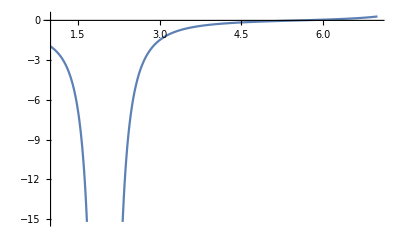

```mathematica
Dα=D[αminmax3, r];
Plot[(%/.{M->1,Q->2}),{r,1,7}]
```

```mathematica
assumptions=r>.5&&r<1.2;
NMinimize[{(αminmax3/.parameter//FullSimplify),assumptions},r]
```

{1.00712,{r→0.854509}}

```mathematica
Limit[αminmax3,r->∞]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1

{5.08372×10^-40,{r→1.80149×10^9}}

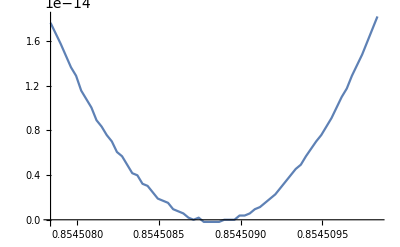

```mathematica
assumptions=r>0;
parameter={M->1,Q->.5,α->1.0071215317999305};
NMinimize[{𝒢Mα3/.parameter,assumptions},r]
Plot[𝒢Mα3/.parameter,{r,0.8545088365540702-.000001,0.8545088365540702+.000001},PlotPoints->2]
```

α solo puede estar entre 1 y 1.0071215317999305 (para Q=0.5), de lo contrario 𝒢Mα3 se hace negativa en algún punto

#### Condición 2

```mathematica
𝒢Mα2=Cond2[Mα]//FullSimplify
%/.α->1//FullSimplify
```

Q^2 r^3 (-(12 r^2 (-1+α))/((Q^2+r^2)^4)+(5 (-3 M+2 √(Q^2+r^2)) (-1+α))/((Q^2+r^2)^(7/2))+(256 M^7 r α)/((Q^6+8 M^3 r^3)^(7/3)))

(256 M^7 Q^2 r^4)/((Q^6+8 M^3 r^3)^(7/3))

1.53155×10^-9

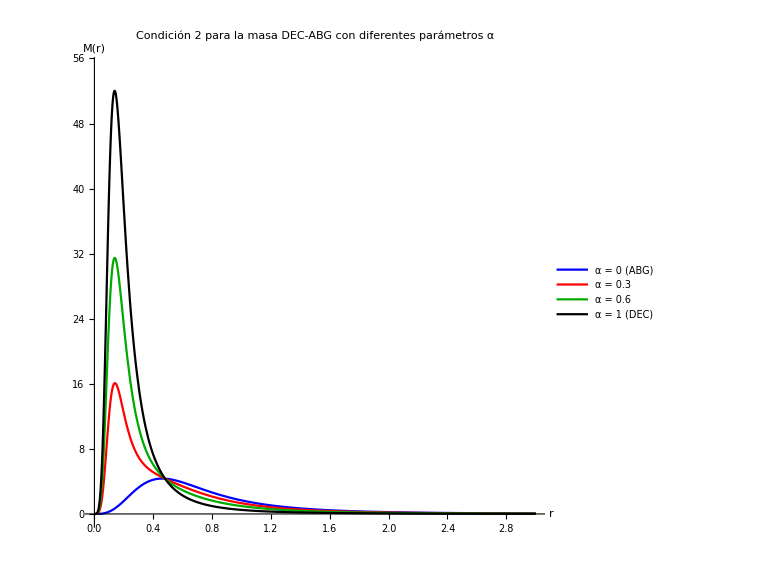
-Graphics-M = 1, Q = 0.5

```mathematica
parameter={M->1,Q->0.5};
alfas={0,.3,.6,1};
titulo="Condición 2 para la masa DEC-ABG con diferentes parámetros α";
leyenda={StringReplace["α = Xα (ABG)",{"Xα"->ToString[alfas[[1]]]}],StringReplace["α = Xα",{"Xα"->ToString[alfas[[2]]]}],StringReplace["α = Xα",{"Xα"->ToString[alfas[[3]]]}],StringReplace["α = Xα (DEC)",{"Xα"->ToString[alfas[[4]]]}]};
label=StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}];
style={{Blue},{Red},{Darker@Green},Black};
plotF={𝒢Mα2/.parameter/.α->alfas[[1]],𝒢Mα2/.parameter/.α->alfas[[2]],𝒢Mα2/.parameter/.α->alfas[[3]],𝒢Mα2/.parameter/.α->alfas[[4]]};
rMin=r/.NMinimize[{𝒢Mα2/.parameter/.α->0,r>0&&r<.0001},r][[2]]

ini=0;
fin=3;
Labeled[Plot[plotF,{r,ini,fin},PlotRange->{-.5,55},AspectRatio->1,PlotStyle->style,PlotLabel->titulo,PlotLegends->leyenda,AxesLabel->{"r","M(r)"},ImageSize->Large],label]
Export["Masa_2cond_mezcla_alfa.png",%,"PNG"];
```

(-(12 Q^2 r^5)/((Q^2+r^2)^4)+(5 Q^2 r^3 (-3 M+2 √(Q^2+r^2)))/((Q^2+r^2)^(7/2)))/(-(12 Q^2 r^5)/((Q^2+r^2)^4)+(256 M^7 Q^2 r^4)/((Q^6+8 M^3 r^3)^(7/3))+(5 Q^2 r^3 (-3 M+2 √(Q^2+r^2)))/((Q^2+r^2)^(7/2)))

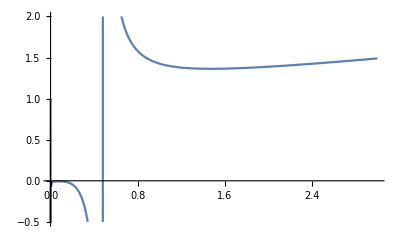

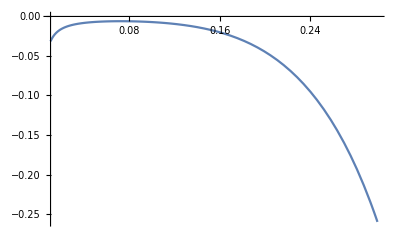

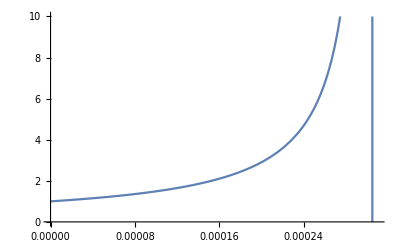

```mathematica
parameter={M->1,Q->.5};
αminmax2=α/.NSolve[𝒢Mα2==0,α][[1]]//Rationalize
Plot[αminmax2/.parameter,{r,0,3},PlotRange->{-.5,2}]
Plot[αminmax2/.parameter,{r,.01,.3}]
Plot[αminmax2/.parameter,{r,0,.00031},PlotRange->{0,10}]
```

(-(12 Q^2 r^5)/((Q^2+r^2)^4)+(5 Q^2 r^3 (-3 M+2 √(Q^2+r^2)))/((Q^2+r^2)^(7/2)))/(-(12 Q^2 r^5)/((Q^2+r^2)^4)+(256 M^7 Q^2 r^4)/((Q^6+8 M^3 r^3)^(7/3))+(5 Q^2 r^3 (-3 M+2 √(Q^2+r^2)))/((Q^2+r^2)^(7/2)))

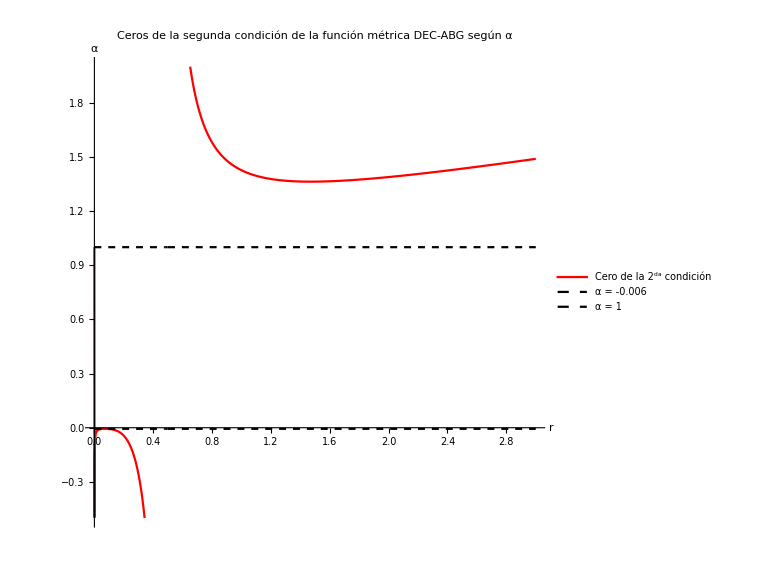
-Graphics-M = 1, Q = 0.5

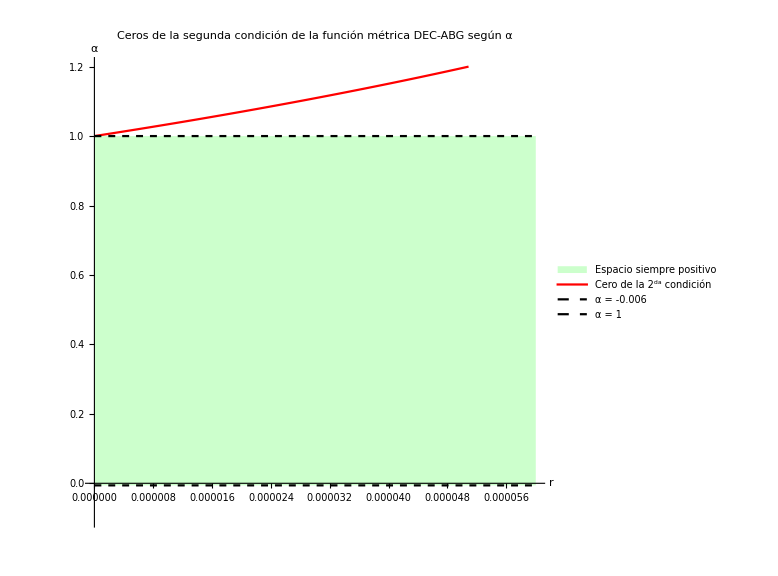
-Graphics-M = 1, Q = 0.5

```mathematica
parameter={M->1,Q->.5};
αminmax2=α/.NSolve[𝒢Mα2==0,α][[1]]//Rationalize

Labeled[Plot[{αminmax2/.parameter,-0.006010814581749652, 1},{r,0,3},PlotRange->{-.5,2},PlotStyle->{Red,{Black,Dashed},{Black,Dashed}},Exclusions->{(αminmax2/.parameter)==10},AspectRatio->1,PlotLegends->{"Cero de la 2^da condición","α = -0.006","α = 1"},PlotLabel->"Ceros de la segunda condición de la función métrica DEC-ABG según α",AxesLabel->{"r","α"},ImageSize->Large],StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}]]
Export["Soluciones_2daCond_Alfa_Mezcla.png",%,"PNG"];

Legended[Labeled[Plot[{αminmax2/.parameter,-0.006010814581749652, 1},{r,0,.00006},PlotRange->{-.1,1.2},PlotStyle->{Red,{Black,Dashed},{Black,Dashed}},Filling->{2->{{3},Opacity[0.2,Green]}},Exclusions->{(αminmax2/.parameter)==10},AspectRatio->1,PlotLabel->"Ceros de la segunda condición de la función métrica DEC-ABG según α",AxesLabel->{"r","α"},ImageSize->Large],StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}]],Placed[Column@{SwatchLegend[{Opacity[.2,Green]},{"Espacio siempre positivo"}],LineLegend[{Red,{Black,Dashed},{Black,Dashed}},{"Cero de la 2^da condición","α = -0.006","α = 1"}]},Right]]
Export["Soluciones_2daCond_Alfa_Mezcla_Zoom.png",%,"PNG"];
```

```mathematica
Limit[αminmax2,r->∞]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

∞

```mathematica
assumptions=r>.01&&r<.3;
NMaximize[{(αminmax2/.parameter//FullSimplify),assumptions},r]
```

{-0.00601081,{r→0.0721421}}

```mathematica
assumptions=r>.9&&r<2;
NMinimize[{(αminmax2/.parameter//FullSimplify),assumptions},r]
```

{1.36291,{r→1.47087}}

```mathematica
assumptions=r>0&&r<.0001;
NMinimize[{(αminmax2/.parameter//FullSimplify),assumptions},r]
```

{1.,{r→0.}}

{2.6359×10^-16,{r→1.47087}}

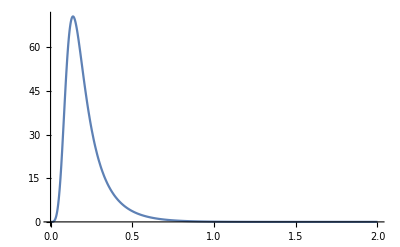

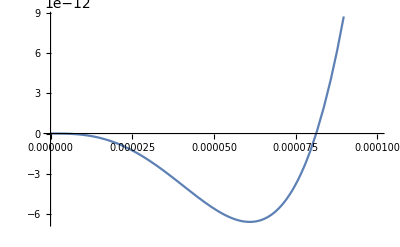

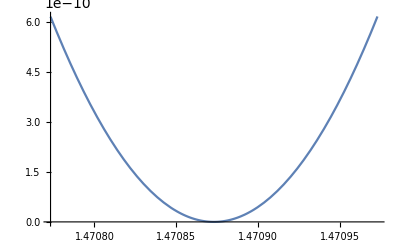

```mathematica
parameter={M->1,Q->.5,α->1.3629096039356723};
assumptions=r>0;
NMinimize[{𝒢Mα2/.parameter,assumptions},r]
Plot[𝒢Mα2/.parameter,{r,0,2},PlotRange->All]
Plot[𝒢Mα2/.parameter,{r,0,.0001}]
Plot[𝒢Mα2/.parameter,{r,1.470873124625008-.0001,1.470873124625008+.0001}]
```

{7.02572×10^-132,{r→4.84693×10^43}}

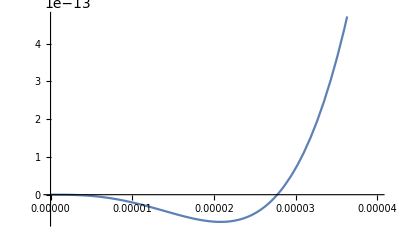

```mathematica
parameter={M->1,Q->.5,α->1.1};
assumptions=r>0;
NMinimize[{𝒢Mα2/.parameter,assumptions},r]
Plot[𝒢Mα2/.parameter,{r,0,.00004}]
```

α debe ser mayor a -0.00601081 y menor a 1 (para Q = 0.5), de lo contrario 𝒢Mα2 se hace negativa en algún punto

## Familias

```mathematica
MDECGen=M(2/(1+Exp[Q^2/(β M r)]))^β
MABGGen=M((1/(1+γ(Q^2/(M r))^α))^(3/α)-Q^2/(2 M r)(1/(1+γ(Q^2/(M r))^α))^(4/α))//FullSimplify
```

2^β (1/(1+ⅇ^(Q^2/(M r β))))^β M

-1/2 M (1/(1+Q^(2 α) (M r)^-α γ))^(3/α) (-2+Q^2 (1/((M r)^α+Q^(2 α) γ))^(1/α))

```mathematica
MABGGen/.{α->2,γ->M^2/Q^2}//FullSimplify
MABG//FullSimplify
```

-(r^3 (Q^2-2 M √(Q^2+r^2)))/(2 (Q^2+r^2)^2)

-(r^3 (Q^2-2 M √(Q^2+r^2)))/(2 (Q^2+r^2)^2)

```mathematica
Limit[MABGGen/.γ->M^2/Q^2,α->∞]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

ConditionalExpression[M-Q^2/(2 r), Log[Q]>0&&2 Log[Q]<Log[M r]&&Log[M r]>0]

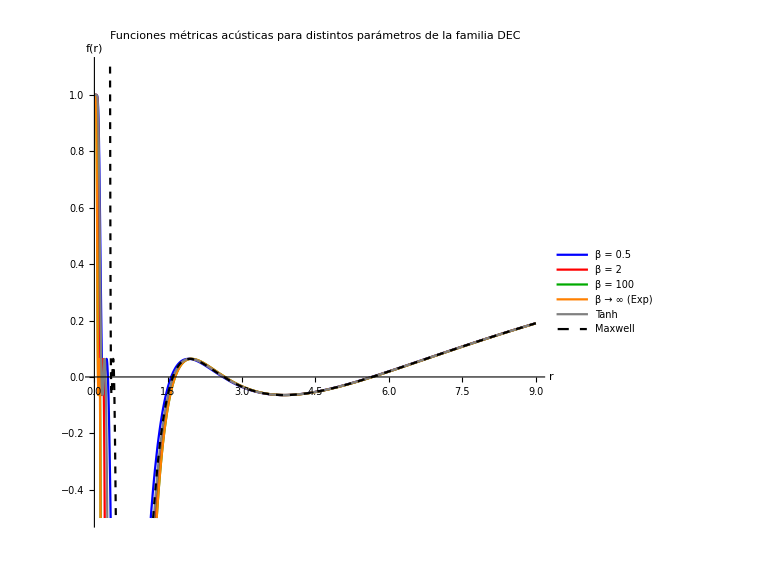
-Graphics-M = 1, Q = 0.8, ξ = 4.5

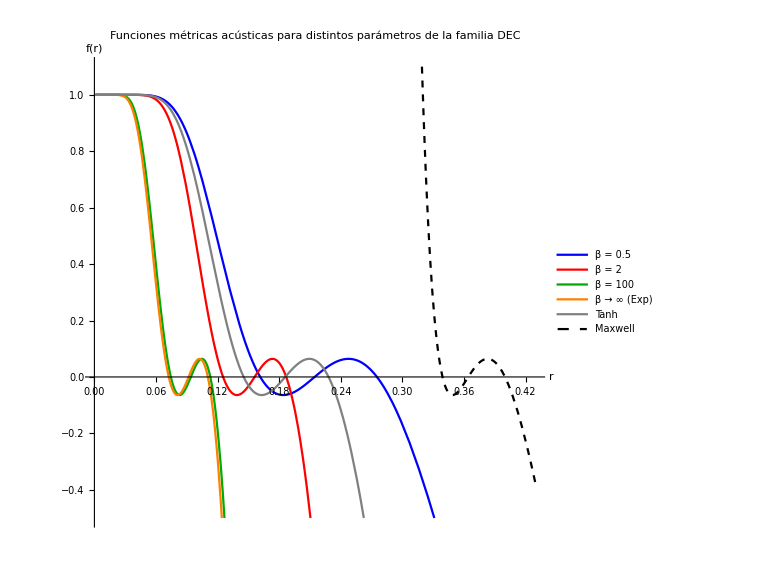
-Graphics-M = 1, Q = 0.8, ξ = 4.5

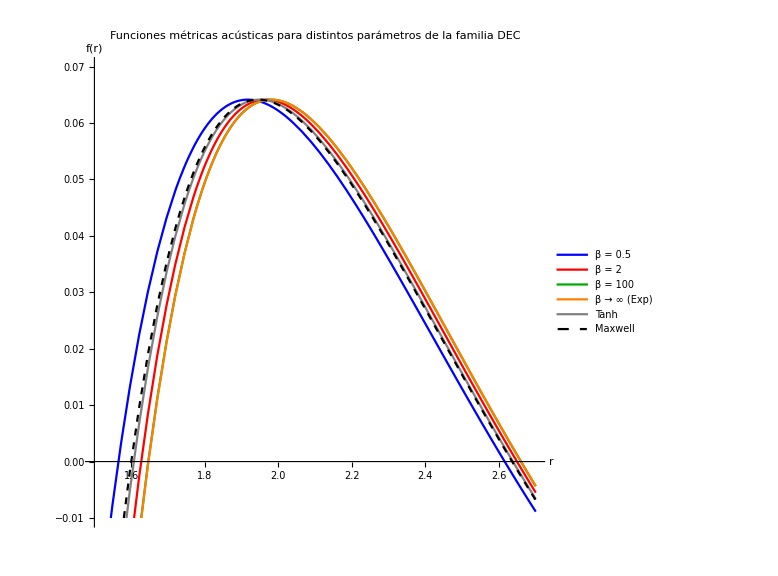
-Graphics-M = 1, Q = 0.8, ξ = 4.5

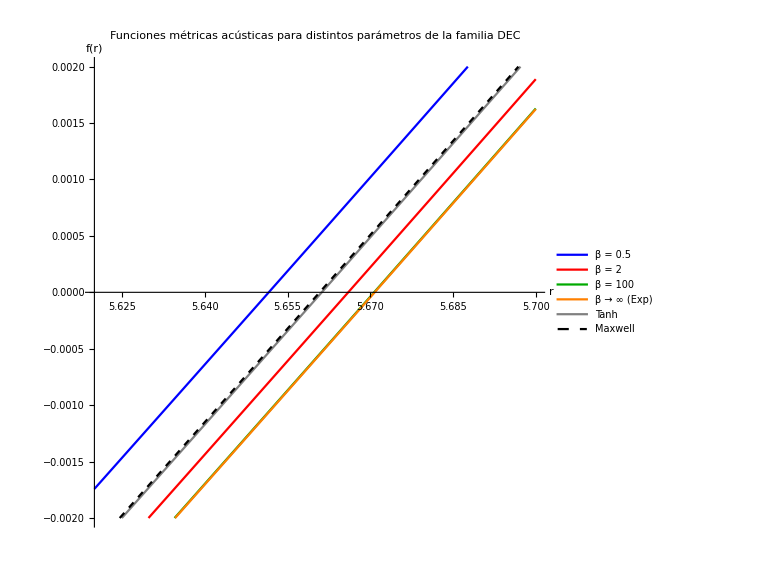
-Graphics-M = 1, Q = 0.8, ξ = 4.5

```mathematica
parameter={M->1,Q->0.8,ξ->4.5};
betas={.5,2,100};
titulo="Funciones métricas acústicas para distintos parámetros de la familia DEC";
leyenda={StringReplace["β = Xβ",{"Xβ"->ToString[betas[[1]]]}],StringReplace["β = Xβ",{"Xβ"->ToString[betas[[2]]]}],StringReplace["β = Xβ",{"Xβ"->ToString[betas[[3]]]}],"β → ∞ (Exp)","Tanh","Maxwell"};
label=StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}];
style={{Blue},{Red},{Darker@Green},{Orange},{Gray},{Dashed,Black}};
plotF={ℱ[MDECGen]/.parameter/.β->0.5,ℱ[MDECGen]/.parameter/.β->2,ℱ[MDECGen]/.parameter/.β->100,ℱ[Mexp]/.parameter,ℱ[Mtanh]/.parameter,ℱRNac/.parameter};


ini=.001;
fin=9;
Labeled[Plot[plotF,{r,ini,fin},PlotRange->{-.5,1.1},AspectRatio->1,PlotStyle->style,PlotLabel->titulo,PlotLegends->leyenda,AxesLabel->{"r","f(r)"},ImageSize->Large],label]
Export["Funciones_beta.png",%,"PNG"];
ini=.001;
fin=.43;
Labeled[Plot[plotF,{r,ini,fin},PlotRange->{-.5,1.1},AspectRatio->1,PlotStyle->style,PlotLabel->titulo,PlotLegends->leyenda,AxesLabel->{"r","f(r)"},ImageSize->Large],label]
Export["Funciones_beta_zoom1.png",%,"PNG"];
ini=1.5;
fin=2.7;
Labeled[Plot[plotF,{r,ini,fin},PlotRange->{-.01,.07},AspectRatio->1,PlotStyle->style,PlotLabel->titulo,PlotLegends->leyenda,AxesLabel->{"r","f(r)"},ImageSize->Large],label]
Export["Funciones_beta_zoom2.png",%,"PNG"];
ini=5.62;
fin=5.7;
Labeled[Plot[plotF,{r,ini,fin},PlotRange->{-.002,.002},AspectRatio->1,PlotStyle->style,PlotLabel->titulo,PlotLegends->leyenda,AxesLabel->{"r","f(r)"},ImageSize->Large],label]
Export["Funciones_beta_zoom3.png",%,"PNG"];
```

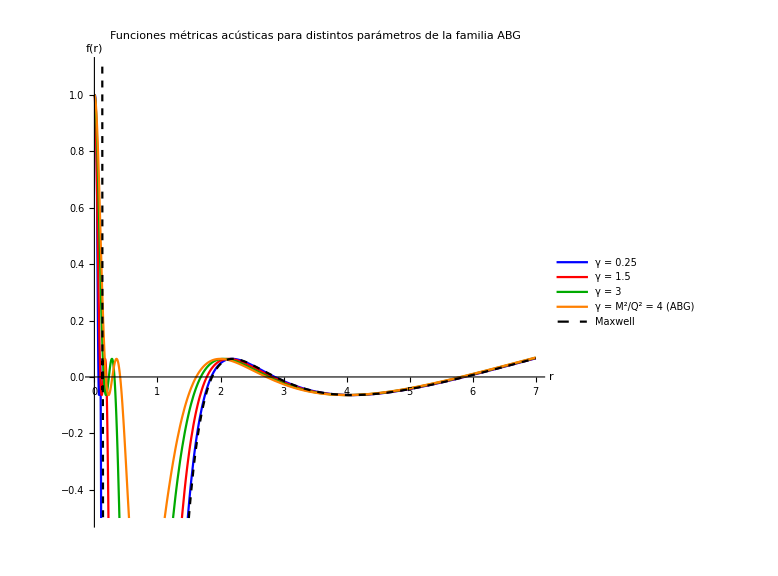
-Graphics-M = 1, Q = 0.5, ξ = 4.5, α = 2

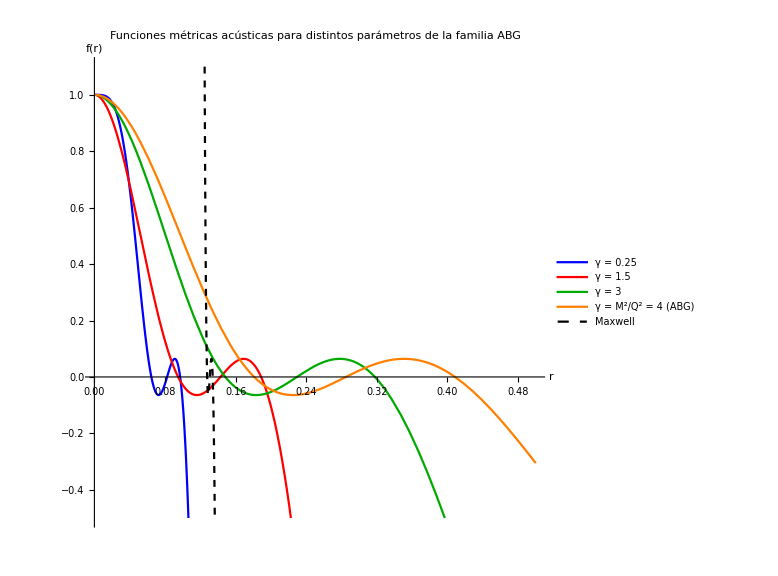
-Graphics-M = 1, Q = 0.5, ξ = 4.5, α = 2

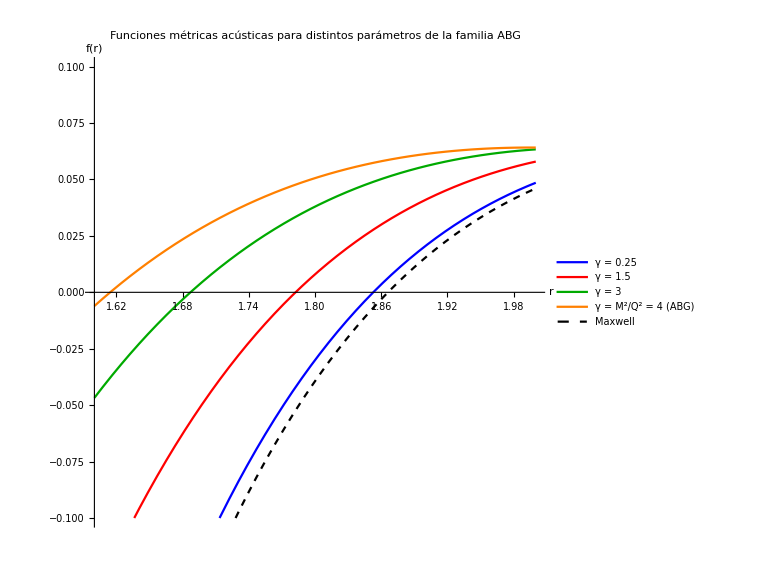
-Graphics-M = 1, Q = 0.5, ξ = 4.5, α = 2

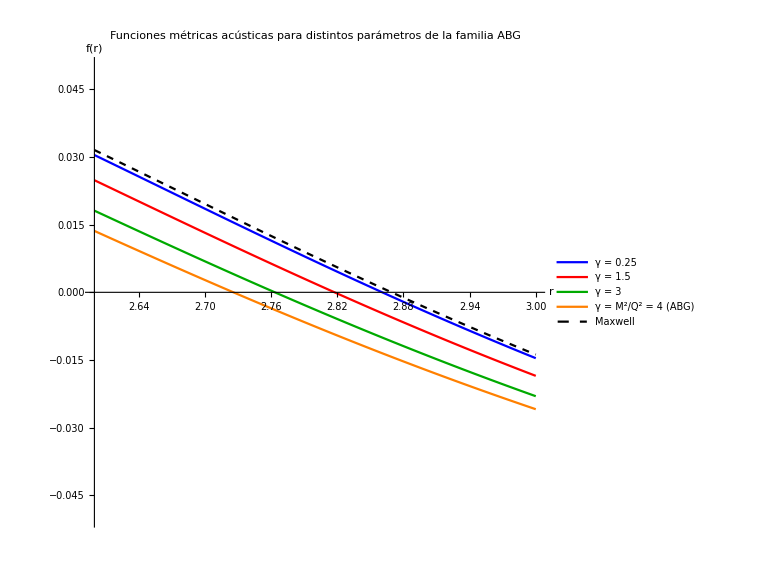
-Graphics-M = 1, Q = 0.5, ξ = 4.5, α = 2

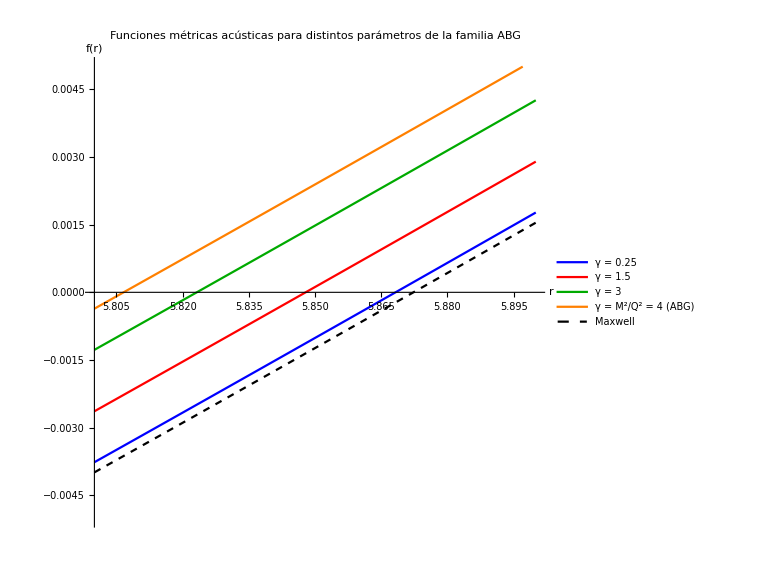
-Graphics-M = 1, Q = 0.5, ξ = 4.5, α = 2

```mathematica
parameter={M->1,Q->0.5,ξ->4.5,α->2};
gammas={.25,1.5,3};
titulo="Funciones métricas acústicas para distintos parámetros de la familia ABG";
leyenda={StringReplace["γ = Xγ",{"Xγ"->ToString[gammas[[1]]]}],StringReplace["γ = Xγ",{"Xγ"->ToString[gammas[[2]]]}],StringReplace["γ = Xγ",{"Xγ"->ToString[gammas[[3]]]}],"γ = M^2/Q^2 = 4 (ABG)","Maxwell"};
label=StringReplace["M = XM, Q = XQ, ξ = Xξ, α = Xα",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]],"Xα"->ToString[α/.parameter[[4]]]}];
style={{Blue},{Red},{Darker@Green},{Orange},{Dashed,Black}};
plotF={ℱ[MABGGen]/.parameter/.γ->gammas[[1]],ℱ[MABGGen]/.parameter/.γ->gammas[[2]],ℱ[MABGGen]/.parameter/.γ->gammas[[3]],ℱ[MABG]/.parameter,ℱRNac/.parameter};


ini=.001;
fin=7;
Labeled[Plot[plotF,{r,ini,fin},PlotRange->{{-.5,1.1}},AspectRatio->1,PlotStyle->style,PlotLabel->titulo,PlotLegends->leyenda,AxesLabel->{"r","f(r)"},ImageSize->Large],label]
Export["Funciones_gamma.png",%,"PNG"];
ini=.001;
fin=.5;
Labeled[Plot[plotF,{r,ini,fin},PlotRange->{{-.5,1.1}},AspectRatio->1,PlotStyle->style,PlotLabel->titulo,PlotLegends->leyenda,AxesLabel->{"r","f(r)"},ImageSize->Large],label]
Export["Funciones_gamma_zoom1.png",%,"PNG"];
ini=1.6;
fin=2;
Labeled[Plot[plotF,{r,ini,fin},PlotRange->{{-.1,.1}},AspectRatio->1,PlotStyle->style,PlotLabel->titulo,PlotLegends->leyenda,AxesLabel->{"r","f(r)"},ImageSize->Large],label]
Export["Funciones_gamma_zoom2.png",%,"PNG"];
ini=2.6;
fin=3;
Labeled[Plot[plotF,{r,ini,fin},PlotRange->{{-.05,.05}},AspectRatio->1,PlotStyle->style,PlotLabel->titulo,PlotLegends->leyenda,AxesLabel->{"r","f(r)"},ImageSize->Large],label]
Export["Funciones_gamma_zoom3.png",%,"PNG"];
ini=5.8;
fin=5.9;
Labeled[Plot[plotF,{r,ini,fin},PlotRange->{{-.005,.005}},AspectRatio->1,PlotStyle->style,PlotLabel->titulo,PlotLegends->leyenda,AxesLabel->{"r","f(r)"},ImageSize->Large],label]
Export["Funciones_gamma_zoom4.png",%,"PNG"];
```

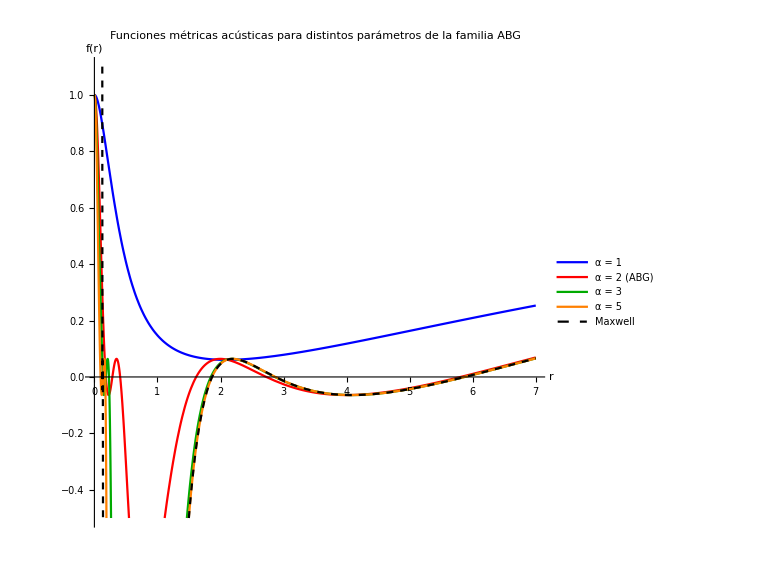
-Graphics-M = 1, Q = 0.5, ξ = 4.5, γ = 4.

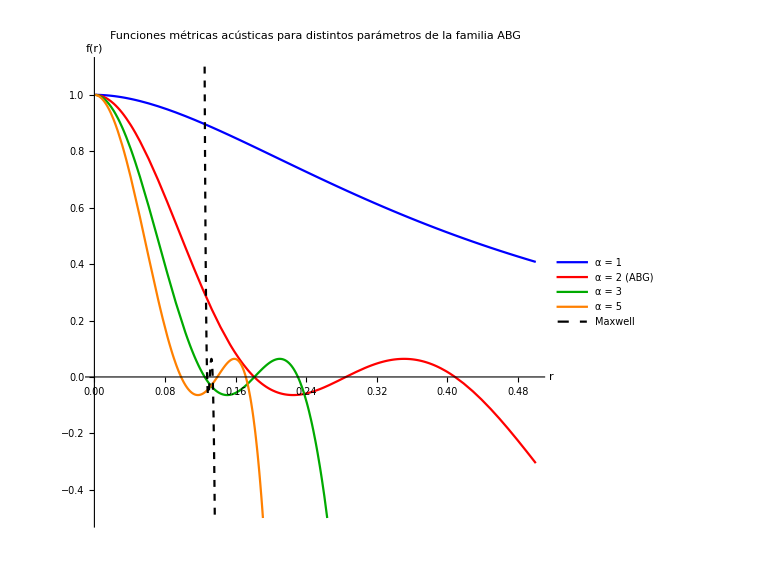
-Graphics-M = 1, Q = 0.5, ξ = 4.5, γ = 4.

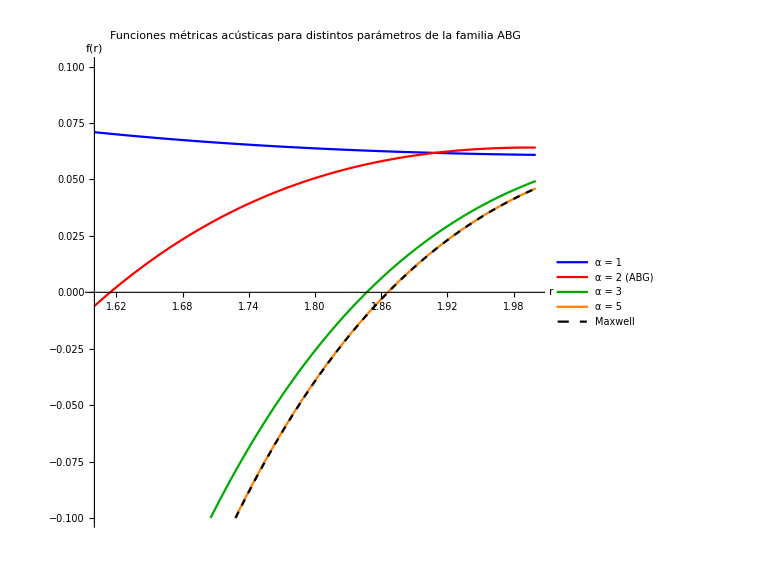
-Graphics-M = 1, Q = 0.5, ξ = 4.5, γ = 4.

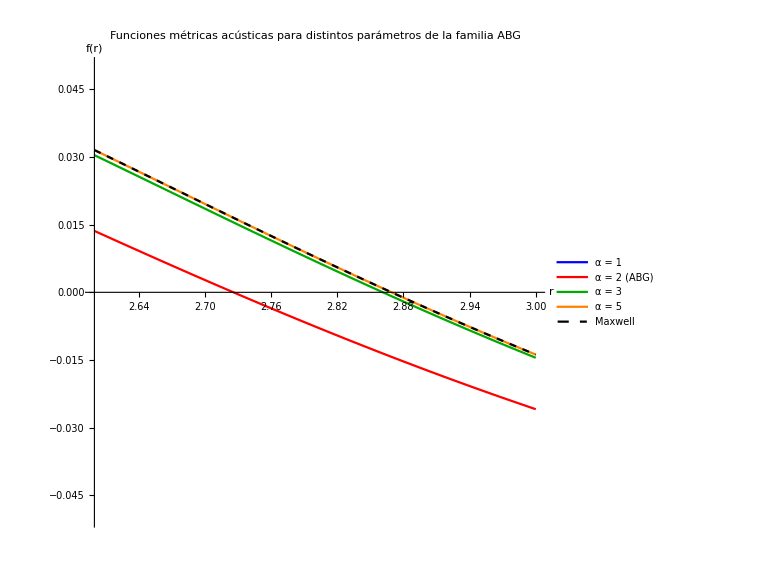
-Graphics-M = 1, Q = 0.5, ξ = 4.5, γ = 4.

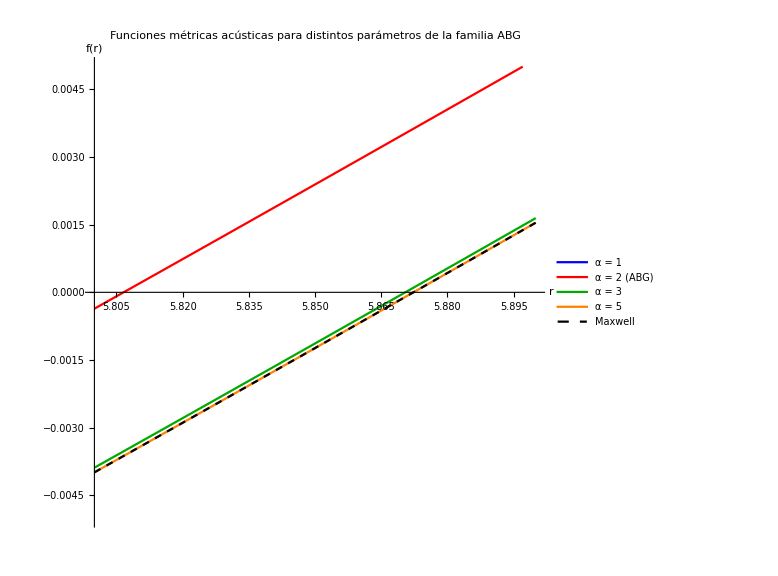
-Graphics-M = 1, Q = 0.5, ξ = 4.5, γ = 4.

```mathematica
parameter={M->MX,Q->QX,ξ->4.5,γ->MX^2/QX^2}/.{MX->1,QX->0.5};
alfas={1,3,5};
titulo="Funciones métricas acústicas para distintos parámetros de la familia ABG";
leyenda={StringReplace["α = Xα",{"Xα"->ToString[alfas[[1]]]}],"α = 2 (ABG)",StringReplace["α = Xα",{"Xα"->ToString[alfas[[2]]]}],StringReplace["α = Xα",{"Xα"->ToString[alfas[[3]]]}],"Maxwell"};
label=StringReplace["M = XM, Q = XQ, ξ = Xξ, γ = Xγ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]],"Xγ"->ToString[γ/.parameter[[4]]]}];
style={{Blue},{Red},{Darker@Green},{Orange},{Dashed,Black}};
plotF={ℱ[MABGGen]/.parameter/.α->alfas[[1]],ℱ[MABG]/.parameter,ℱ[MABGGen]/.parameter/.α->alfas[[2]],ℱ[MABGGen]/.parameter/.α->alfas[[3]],ℱRNac/.parameter};


ini=.001;
fin=7;
Labeled[Plot[plotF,{r,ini,fin},PlotRange->{{-.5,1.1}},AspectRatio->1,PlotStyle->style,PlotLabel->titulo,PlotLegends->leyenda,AxesLabel->{"r","f(r)"},ImageSize->Large],label]
Export["Funciones_alfa.png",%,"PNG"];
ini=.001;
fin=.5;
Labeled[Plot[plotF,{r,ini,fin},PlotRange->{{-.5,1.1}},AspectRatio->1,PlotStyle->style,PlotLabel->titulo,PlotLegends->leyenda,AxesLabel->{"r","f(r)"},ImageSize->Large],label]
Export["Funciones_alfa_zoom1.png",%,"PNG"];
ini=1.6;
fin=2;
Labeled[Plot[plotF,{r,ini,fin},PlotRange->{{-.1,.1}},AspectRatio->1,PlotStyle->style,PlotLabel->titulo,PlotLegends->leyenda,AxesLabel->{"r","f(r)"},ImageSize->Large],label]
Export["Funciones_alfa_zoom2.png",%,"PNG"];
ini=2.6;
fin=3;
Labeled[Plot[plotF,{r,ini,fin},PlotRange->{{-.05,.05}},AspectRatio->1,PlotStyle->style,PlotLabel->titulo,PlotLegends->leyenda,AxesLabel->{"r","f(r)"},ImageSize->Large],label]
Export["Funciones_alfa_zoom3.png",%,"PNG"];
ini=5.8;
fin=5.9;
Labeled[Plot[plotF,{r,ini,fin},PlotRange->{{-.005,.005}},AspectRatio->1,PlotStyle->style,PlotLabel->titulo,PlotLegends->leyenda,AxesLabel->{"r","f(r)"},ImageSize->Large],label]
Export["Funciones_alfa_zoom4.png",%,"PNG"];
```

## Plot funciones métricas y horizontes según ξ

### Modelos específicos

#### DEC

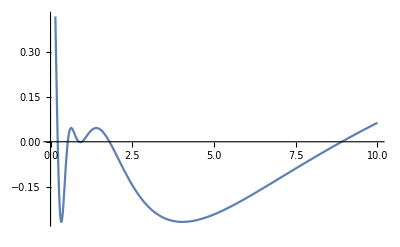

```mathematica
Plot[ℱ[MDEC]/.{M->1,Q->1.025,ξ->6},{r,0,10}]
```

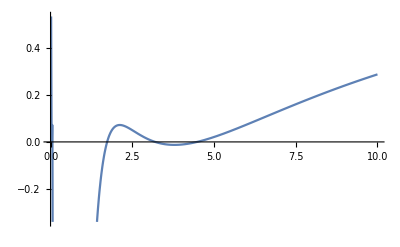

```mathematica
Plot[ℱ[rDEC]/.{M->1,Q->0.5,ξ->4.1},{r,0,10}]
```

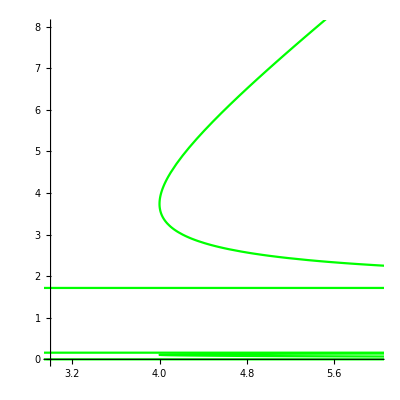

```mathematica
parameter={M->1,Q->0.7,ξ->5};
ξDEC=ξ/.Solve[ℱ[MDEC]==0,ξ]//FullSimplify;
DECsolPlot=ParametricPlot[{ξDEC[[1]]/.parameter,r},{r,0,10},PlotRange->{{3,6},{0,8}},AspectRatio->1,PlotStyle->{Green}]
```

#### ABG - Perez

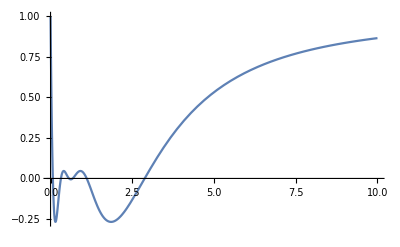

```mathematica
Plot[ℱ[MABG]/.{M->1,Q->0.875,ξ->6},{r,0,10}]
```

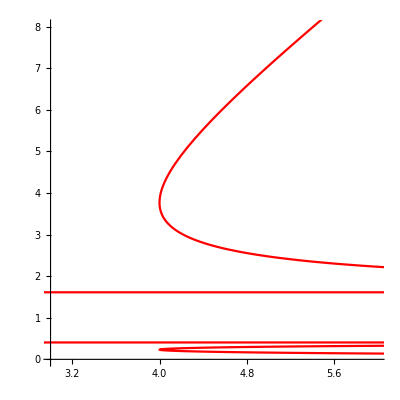

```mathematica
parameter={M->1,Q->0.5,ξ->5};
ξABG=ξ/.Solve[ℱ[MABG]==0,ξ]//FullSimplify;
ABGsolPlot=ParametricPlot[{ξABG[[1]]/.parameter,r},{r,0,10},PlotRange->{{3,6},{0,8}},AspectRatio->1,PlotStyle->{Red}]
```

#### Tanh

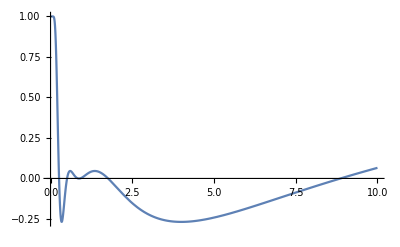

```mathematica
Plot[ℱ[Mtanh]/.{M->1,Q->1.055,ξ->6},{r,0,10},PlotRange->All]
```

```mathematica
parameter={M->1,Q->0.7,ξ->5};
ξtanh=ξ/.Solve[ℱ[Mtanh]==0,ξ]//FullSimplify;
tanhsolPlot=ParametricPlot[{ξtanh[[1]]/.parameter,r},{r,0,10},PlotRange->{{3,6},{0,8}},AspectRatio->1,PlotStyle->{Thin,Blue}]
```

-Graphics-

#### Exp

```mathematica
parameter={M->1,Q->0.7,ξ->5};
ξexp=ξ/.Solve[ℱ[Mexp]==0,ξ]//FullSimplify;
expsolPlot=ParametricPlot[{ξexp[[1]]/.parameter,r},{r,0,10},PlotRange->{{3,6},{0,8}},AspectRatio->1,PlotStyle->{Orange}]
```

-Graphics-

#### Maxwell

```mathematica
Plot[ℱ[MDEC]/.{M->1,Q->1.025,ξ->6},{r,0,10}]
```

```mathematica
Ξ=√(ξ^2-4ξ);
Xξ=2 M^2 ξ^2-4 M^2 ξ-2ξ Q^2;
Yξ=(8 M^3 ξ^3-8M ξ(4 M^2 ξ+ξ Q^2)+32M ξ Q^2)/(4 M √(ξ^2-4ξ));
rc=M-√((M-Q) (M+Q));
rh=M+√((M-Q) (M+Q));
ra1=(M ξ)/2-1/2 M Ξ - 1/2 √(Xξ-Yξ);
ra2=(M ξ)/2-1/2 M Ξ + 1/2 √(Xξ-Yξ);
ra3=(M ξ)/2+1/2 M Ξ - 1/2 √(Xξ+Yξ);
ra4=(M ξ)/2+1/2 M Ξ + 1/2 √(Xξ+Yξ);
ra1Plot=Plot[ra1/.{M->1,Q->1/2},{ξ,3.5,8}];
ra2Plot=Plot[ra2/.{M->1,Q->1/2},{ξ,3.5,8}];
ra3Plot=Plot[ra3/.{M->1,Q->1/2},{ξ,3.5,8}];
ra4Plot=Plot[ra4/.{M->1,Q->1/2},{ξ,3.5,8}];
rcPlot=Plot[rc/.{M->1,Q->1/2},{ξ,3.5,8}];
rhPlot=Plot[rh/.{M->1,Q->1/2},{ξ,3.5,8}];
plotMaxwell=Show[ra1Plot,ra2Plot,ra3Plot,ra4Plot,rcPlot,rhPlot,PlotRange->All];
```

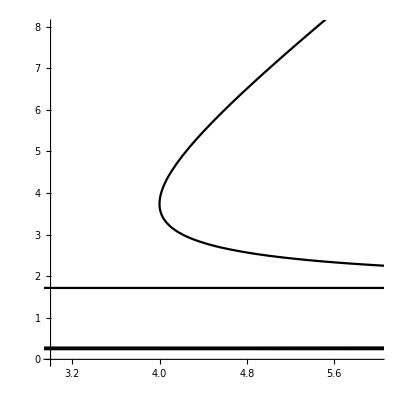

```mathematica
parameter={M->1,Q->0.7,ξ->5};
ξmaxw=ξ/.Solve[ℱRNac==0,ξ]//FullSimplify;
maxwsolPlot=ParametricPlot[{ξmaxw[[1]]/.parameter,r},{r,0,10},PlotRange->{{3,6},{0,8}},AspectRatio->1,PlotStyle->{Black}]
```

### Todos los modelos

Negro=Maxwell, Rojo=DEC, Verde=ABG, Azul=Tanh, Naranjo=exp

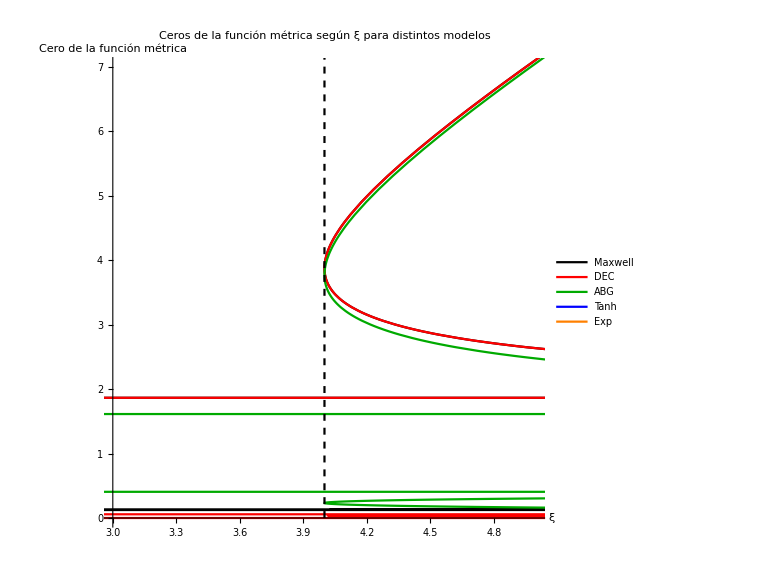
-Graphics-M = 1, Q = 0.5

```mathematica
parameter={M->1,Q->0.5};
Labeled[ParametricPlot[{{ξmaxw[[1]]/.parameter,r},{ξDEC[[1]]/.parameter,r},{ξABG[[1]]/.parameter,r},{ξtanh[[1]]/.parameter,r},{ξexp[[1]]/.parameter,r},{4,r}},{r,0,10},PlotRange->{{3,5},{0,7}},AspectRatio->1,PlotStyle->{{Black},{Red},{Darker@Green},{Blue},{Orange},{Dashed,Black}},PlotLabel->"Ceros de la función métrica según ξ para distintos modelos",PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"ξ","Cero de la función métrica"},ImageSize->Large],StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}]]
Export["Soluciones_Xi_General.png",%,"PNG"];
```

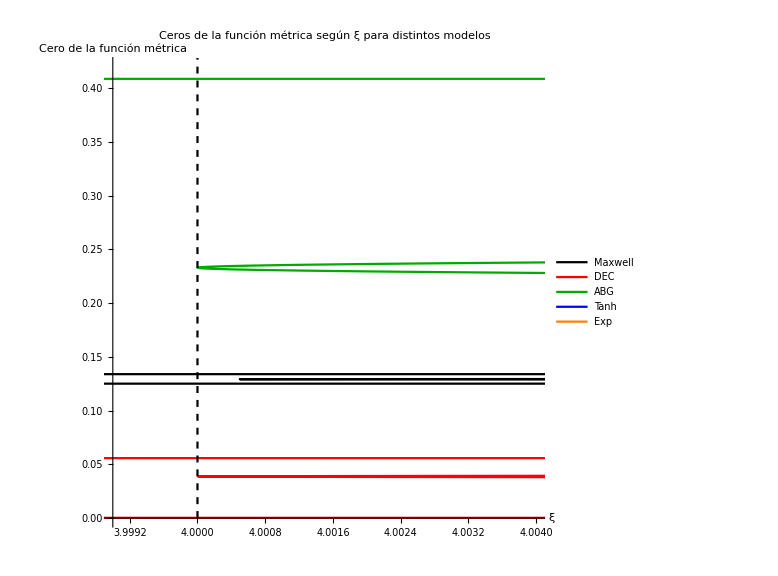
-Graphics-M = 1, Q = 0.5

```mathematica
parameter={M->1,Q->0.5};
Labeled[ParametricPlot[{{ξmaxw[[1]]/.parameter,r},{ξDEC[[1]]/.parameter,r},{ξABG[[1]]/.parameter,r},{ξtanh[[1]]/.parameter,r},{ξexp[[1]]/.parameter,r},{4,r}},{r,0,10},PlotRange->{{3.999,4.004},{0,0.42}},AspectRatio->1,PlotStyle->{{Black},{Red},{Darker@Green},{Blue},{Orange},{Dashed,Black}},PlotPoints->1000,PlotLabel->"Ceros de la función métrica según ξ para distintos modelos",PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"ξ","Cero de la función métrica"},ImageSize->Large],StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}]]
Export["Soluciones_Xi_Zoom1.png",%,"PNG"];
```

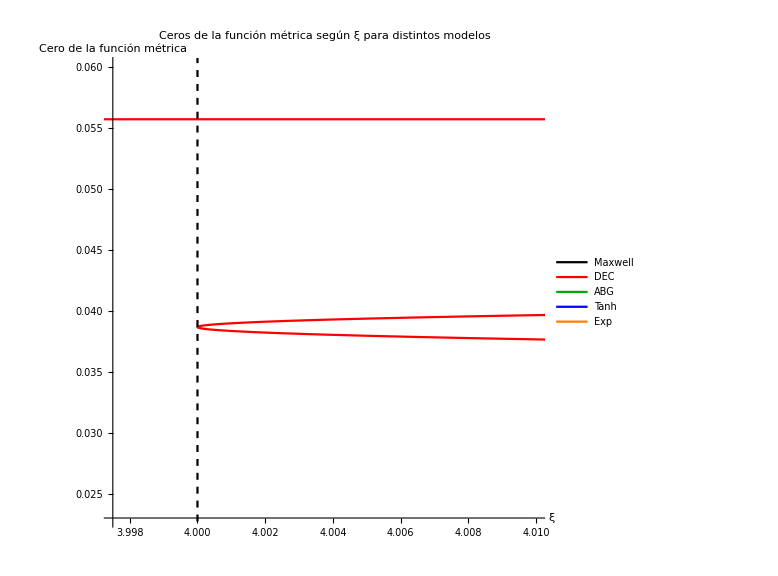
-Graphics-M = 1, Q = 0.5

```mathematica
parameter={M->1,Q->0.5};
Labeled[ParametricPlot[{{ξmaxw[[1]]/.parameter,r},{ξDEC[[1]]/.parameter,r},{ξABG[[1]]/.parameter,r},{ξtanh[[1]]/.parameter,r},{ξexp[[1]]/.parameter,r},{4,r}},{r,0,0.1},PlotRange->{{3.9975,4.01},{0.023,0.06}},AspectRatio->1,PlotStyle->{{Black},{Red},{Darker@Green},{Blue},{Orange},{Dashed,Black}},PlotPoints->1000,PlotLabel->"Ceros de la función métrica según ξ para distintos modelos",PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"ξ","Cero de la función métrica"},ImageSize->Large],StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}]]
Export["Soluciones_Xi_Zoom2.png",%,"PNG"];
```

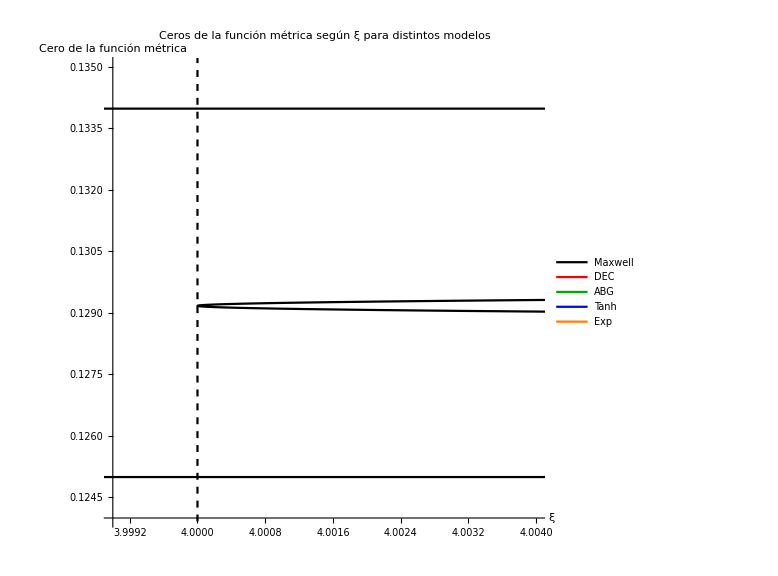
-Graphics-M = 1, Q = 0.5

```mathematica
parameter={M->1,Q->0.5};
Labeled[ParametricPlot[{{ξmaxw[[1]]/.parameter,r},{ξDEC[[1]]/.parameter,r},{ξABG[[1]]/.parameter,r},{ξtanh[[1]]/.parameter,r},{ξexp[[1]]/.parameter,r},{4,r}},{r,0,0.5},PlotRange->{{3.999,4.004},{.124,.135}},AspectRatio->1,PlotStyle->{{Black},{Red},{Darker@Green},{Blue},{Orange},{Dashed,Black}},PlotPoints->3000,PlotLabel->"Ceros de la función métrica según ξ para distintos modelos",PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"ξ","Cero de la función métrica"},ImageSize->Large],StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}]]
Export["Soluciones_Xi_Zoom3.png",%,"PNG"];
```

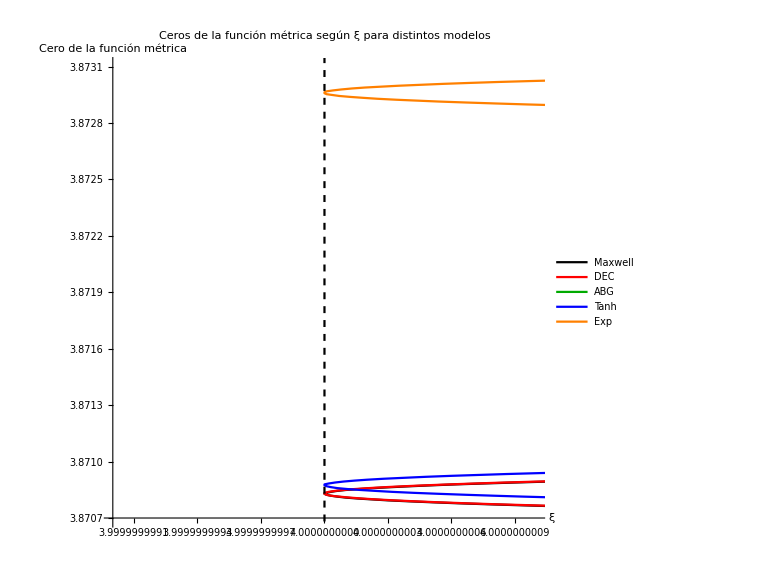
-Graphics-M = 1, Q = 0.5

```mathematica
parameter={M->1,Q->0.5};
Labeled[ParametricPlot[{{ξmaxw[[1]]/.parameter,r},{ξDEC[[1]]/.parameter,r},{ξABG[[1]]/.parameter,r},{ξtanh[[1]]/.parameter,r},{ξexp[[1]]/.parameter,r},{4,r}},{r,3.85,3.9},PlotRange->{{3.999999999,4.000000001},{3.8707,3.8731}},AspectRatio->1,PlotStyle->{{Black},{Red},{Darker@Green},{Blue},{Orange},{Dashed,Black}},PlotPoints->5000,PlotLabel->"Ceros de la función métrica según ξ para distintos modelos",PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"ξ","Cero de la función métrica"},Ticks->{tickfunc,Automatic},ImageSize->Large],StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}]]
Export["Soluciones_Xi_Zoom4.png",%,"PNG"];
```

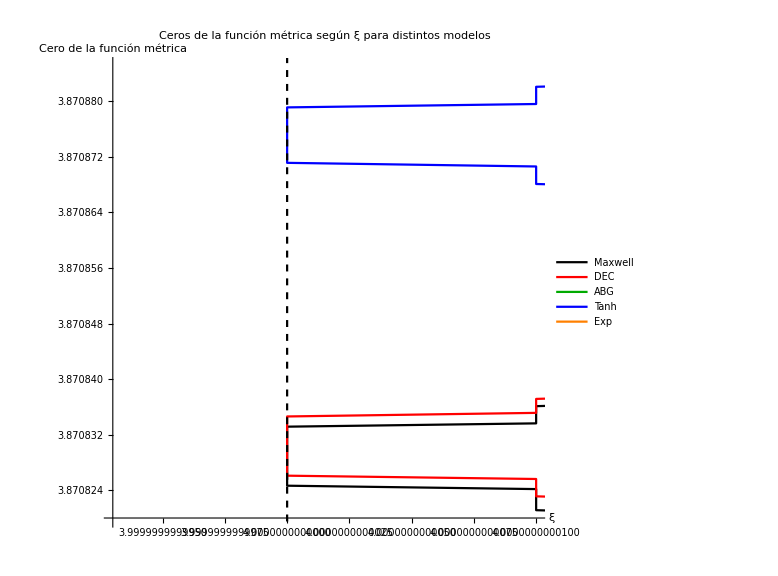
-Graphics-M = 1, Q = 0.5

```mathematica
parameter={M->1,Q->0.5};
Labeled[ParametricPlot[{{ξmaxw[[1]]/.parameter,r},{ξDEC[[1]]/.parameter,r},{ξABG[[1]]/.parameter,r},{ξtanh[[1]]/.parameter,r},{ξexp[[1]]/.parameter,r},{4,r}},{r,3.87,3.875},PlotRange->{{3.999999999993,4.00000000001},{3.87082,3.870885}},AspectRatio->1,PlotStyle->{{Black},{Red},{Darker@Green},{Blue},{Orange},{Dashed,Black}},PlotPoints->5000,PlotLabel->"Ceros de la función métrica según ξ para distintos modelos",PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"ξ","Cero de la función métrica"},Ticks->{tickfunc,Automatic},ImageSize->Large],StringReplace["M = XM, Q = XQ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]]}]]
Export["Soluciones_Xi_Zoom5.png",%,"PNG"];
```

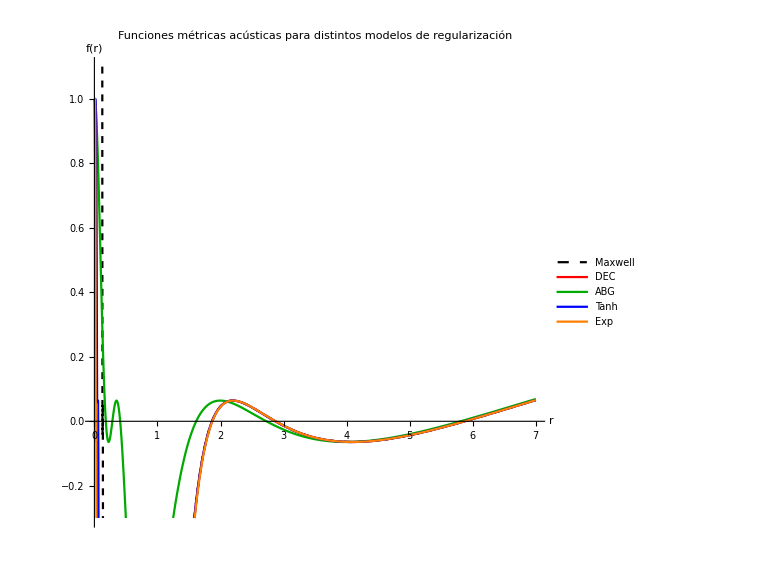
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[MDEC]/.parameter,ℱ[MABG]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,.001,7},PlotRange->{-.3,1.1},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_General.png",%,"PNG"];
```

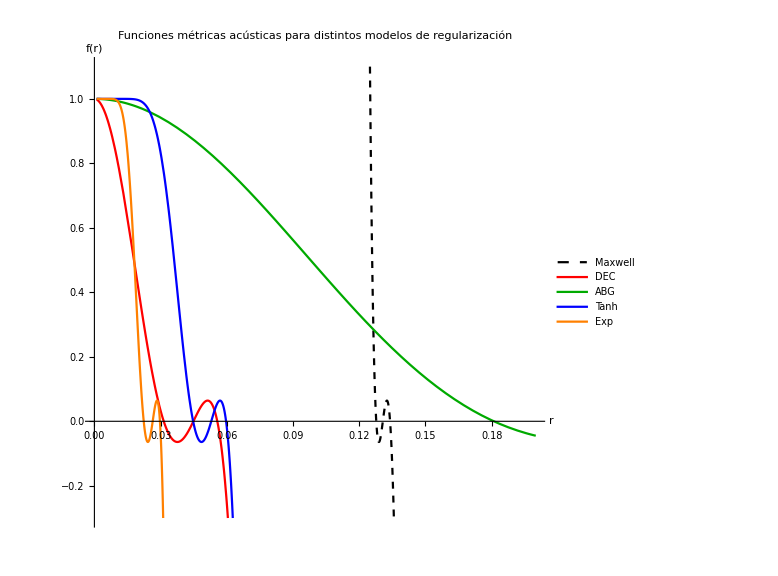
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[MDEC]/.parameter,ℱ[MABG]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,.001,.2},PlotRange->{-.3,1.1},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_Zoom1.png",%,"PNG"];
```

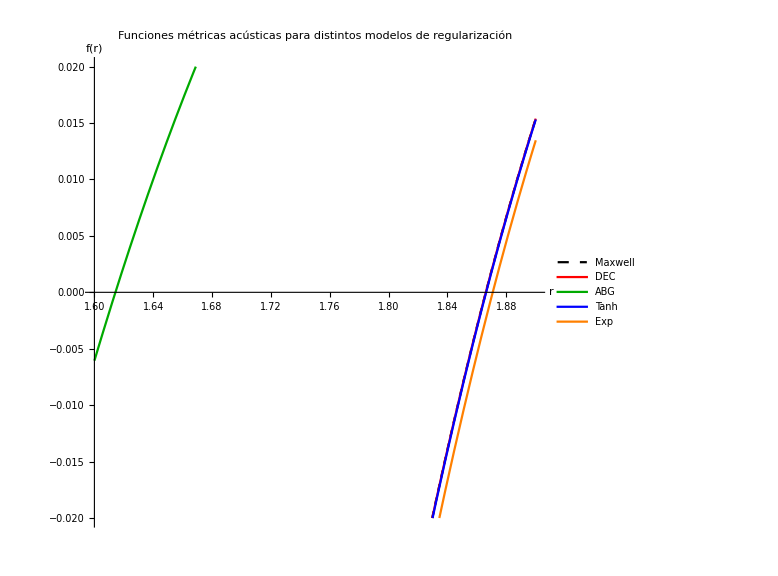
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[MDEC]/.parameter,ℱ[MABG]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,1.6,1.9},PlotRange->{-.02,.02},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_Zoom2.png",%,"PNG"];
```

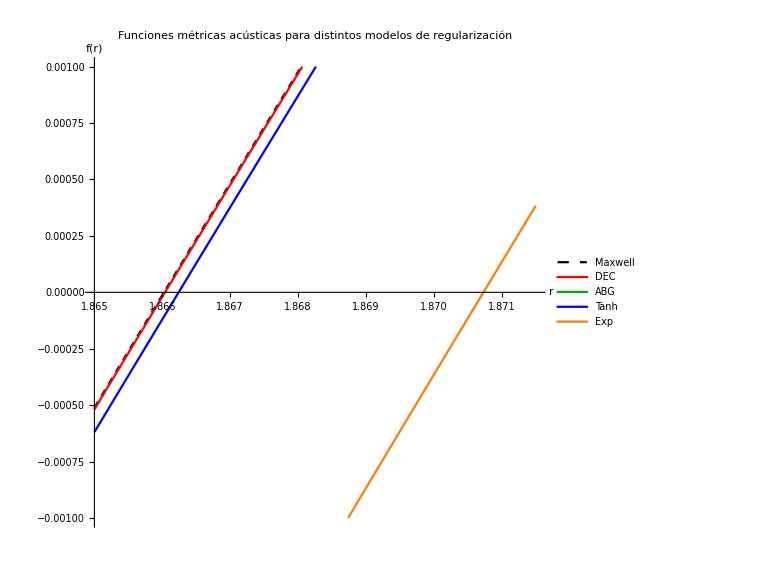
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[MDEC]/.parameter,ℱ[MABG]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,1.865,1.8715},PlotRange->{-.001,.001},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_Zoom3.png",%,"PNG"];
```

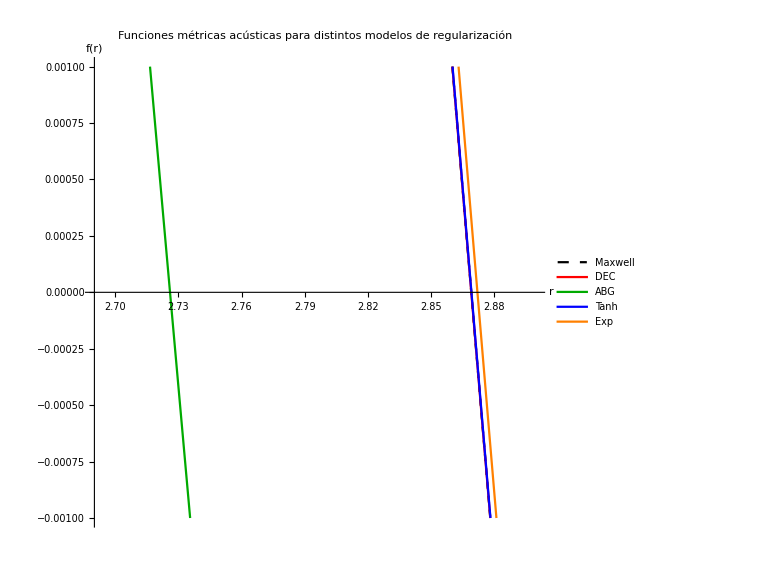
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[MDEC]/.parameter,ℱ[MABG]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,2.69,2.9},PlotRange->{-.001,.001},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_Zoom4.png",%,"PNG"];
```

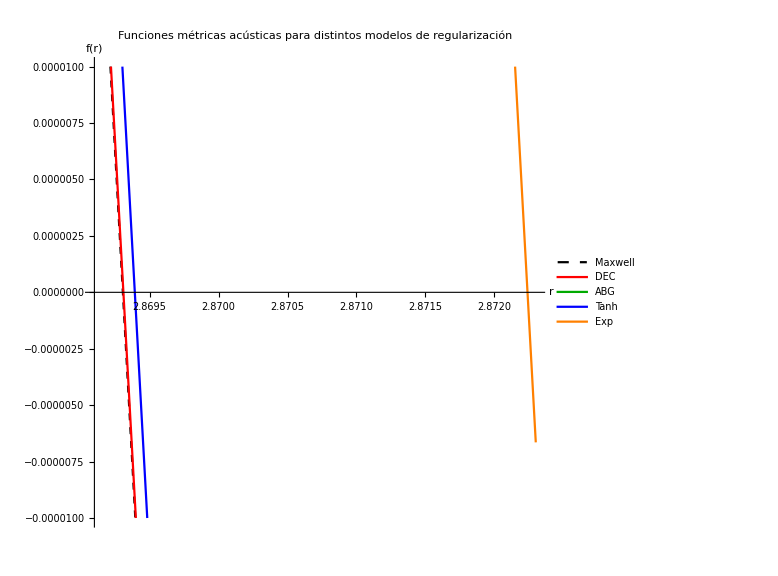
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[MDEC]/.parameter,ℱ[MABG]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,2.8691,2.8723},PlotRange->{-.00001,.00001},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_Zoom5.png",%,"PNG"];
```

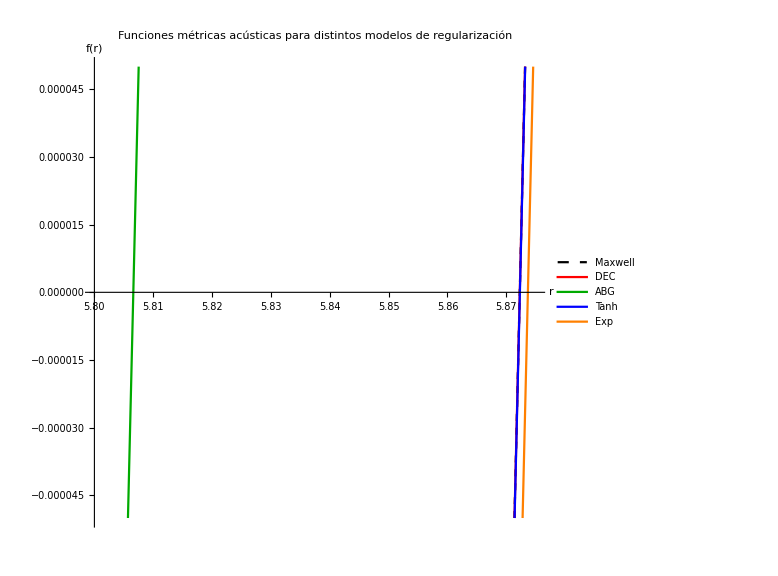
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[MDEC]/.parameter,ℱ[MABG]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,5.8,5.875},PlotRange->{-.00005,.00005},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_Zoom6.png",%,"PNG"];
```

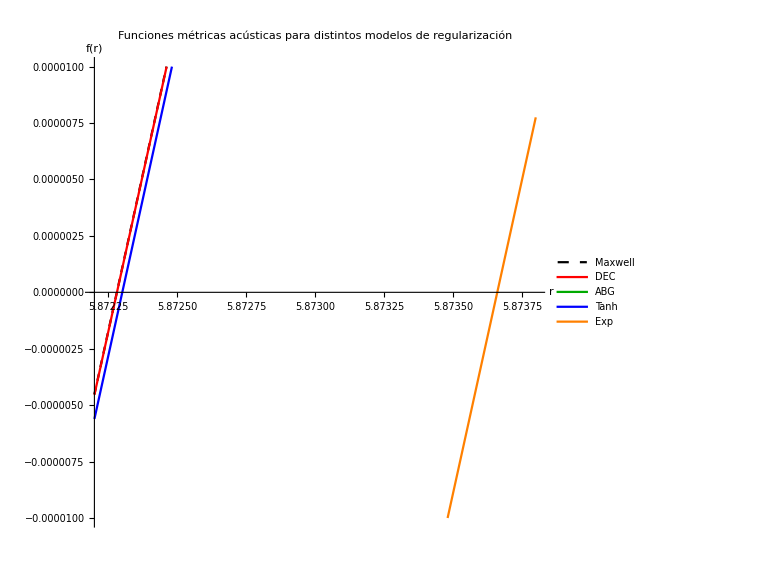
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[MDEC]/.parameter,ℱ[MABG]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,5.8722,5.8738},PlotRange->{-.00001,.00001},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_Zoom7.png",%,"PNG"];
```

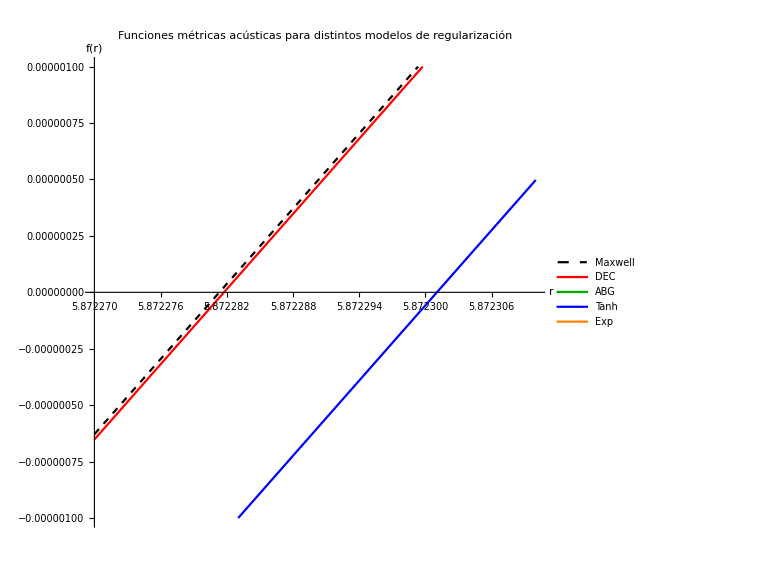
-Graphics-M = 1, Q = 0.5, ξ = 4.5

```mathematica
parameter={M->1,Q->0.5,ξ->4.5};
Labeled[Plot[{ℱRNac/.parameter,ℱ[MDEC]/.parameter,ℱ[MABG]/.parameter,ℱ[Mtanh]/.parameter,ℱ[Mexp]/.parameter},{r,5.87227,5.87231},PlotRange->{-.000001,.000001},AspectRatio->1,PlotLabel->"Funciones métricas acústicas para distintos modelos de regularización",PlotStyle->{{Dashed,Black},Red,Darker@Green,Blue,Orange},PlotLegends->{"Maxwell","DEC","ABG","Tanh","Exp"},AxesLabel->{"r","f(r)"},ImageSize->Large],StringReplace["M = XM, Q = XQ, ξ = Xξ",{"XM"->ToString[M/.parameter[[1]]],"XQ"->ToString[Q/.parameter[[2]]],"Xξ"->ToString[ξ/.parameter[[3]]]}]]
Export["Funciones_Metricas_Zoom8.png",%,"PNG"];
```

## Tabla

```mathematica
Parametros={M->1,Q->0.7,ξ->4.5};
a[1,1]="Modelo";
a[1,2]="Rc";
a[1,3]="Rh";
a[2,1]="Maxwell";
a[3,1]="DEC";
a[4,1]="ABG";
a[5,1]="Tanh";
a[6,1]="Exp";
a[2,2]=r/.NSolve[ℱRNac1/.Parametros,r,PositiveReals];
a[3,2]=r/.NSolve[ℱ1[MDEC]/.Parametros,r,PositiveReals];
a[4,2]=r/.NSolve[ℱ1[MABG]/.Parametros,r,PositiveReals];
a[5,2]=r/.NSolve[ℱ1[Mtanh]/.Parametros,r,PositiveReals];
a[6,2]=r/.NSolve[ℱ1[Mexp]/.Parametros,r,PositiveReals];
a[2,3]=r/.NSolve[ℱRNac2/.Parametros,r,PositiveReals];
a[3,3]=r/.NSolve[ℱ2[MDEC]/.Parametros,r,PositiveReals];
a[4,3]=r/.NSolve[ℱ2[MABG]/.Parametros,r,PositiveReals];
a[5,3]=r/.NSolve[ℱ2[Mtanh]/.Parametros,r,PositiveReals];
a[6,3]=r/.NSolve[ℱ2[Mexp]/.Parametros,r,PositiveReals];
TableForm[Flatten@Array[a,{6,3}][[#]]&/@Range[Length@Array[a,{6,3}]]]
```

Modelo | Rc | Rh |  |  |  | 
Maxwell | 0.285857 | 1.71414 | 0.255915 | 0.269147 | 2.73085 | 5.74408
DEC | 0.161787 | 1.71448 | 0.087015 | 0.126653 | 2.73093 | 5.74409
ABG | 0.191006 | 1.09275 | 0.0577513 | 0.119355 | 1.49195 | 2.29087
Tanh | 0.151463 | 1.71645 | 0.103219 | 0.128101 | 2.73165 | 5.74425
Exp | 0.0744508 | 1.73688 | 0.0514911 | 0.0635654 | 2.74373 | 5.74971